```mathematica
rcut=0.03 ;
c200=29.68;
rhos1=8.87063 10^7;
rs1=7.14802;
rhonfw[r_]:=rhos1/((r/rs1)(1+r/rs1)^2); 
rhocut[r_]:=rhos1/((r/rs1)(1+r/rs1)^2)Exp[-r/rcut]/(1+rs1/rcut)^0.3;
rhonfwsmall[r_]:=(4.377 10^10)/((r/0.011)(1+r/0.011)^2);
rhojaffe[r_]:=(4.32 10^7)/((r/0.149)^2((r/0.149)^2+1));
```

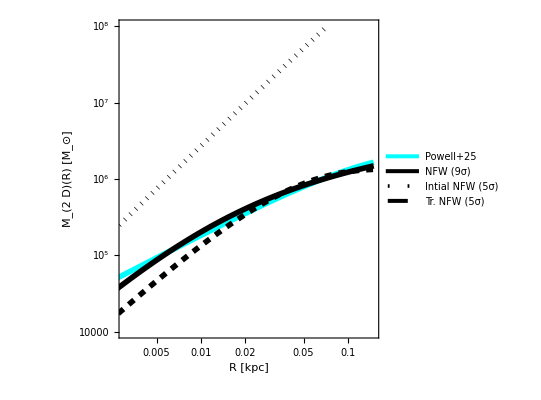

```mathematica
mnfw2d[rr_]:=2π NIntegrate[rhonfw[√(rrr^2+z^2)]rrr,{z,-c200 rs1,+c200 rs1},{rrr,0,rr}];
mnfwsmall2d[rr_]:=2π NIntegrate[rhonfwsmall[√(rrr^2+z^2)]rrr,{z,-295 0.01,+295 0.01},{rrr,0,rr}];
mcut2d[rr_]:=2π NIntegrate[rhocut[√(rrr^2+z^2)]rrr,{z,-c200 rs1,+c200 rs1},{rrr,0,rr}];
mjaff2d[rr_]:=2π NIntegrate[rhojaffe[√(rrr^2+z^2)]rrr,{z,-c200 rs1,+c200 rs1},{rrr,0,rr}];
LogLogPlot[{mjaff2d[x],mnfwsmall2d[x],mnfw2d[x],mcut2d[x]},{x,0.001,0.15},PlotStyle->{{Cyan,Thickness[0.01]},{Black,Thickness[0.01]},{Dotted,Black,Thickness[0.009]},{Black,Dashed,Thickness[0.01]}},Frame->True,FrameLabel->{"R [kpc]","M_(2  D)(R) [M_(<⊙>)]"},PlotRange->{{0.003,0.15 },{10^4,10^8}},PlotLegends->Placed[LineLegend[{"Powell+25","NFW (9σ)","Intial NFW (5σ)","Tr. NFW (5σ)"},LegendMarkerSize->{25,7} ,LabelStyle->11,LegendLayout->{"Column",1}],{0.18,0.85}],FrameStyle->Directive[Black,Thickness[0.003]],TicksStyle->Large,LabelStyle->Directive[Black,13],AspectRatio->1]
```

```mathematica
ρHern[ρH_,rH_,r_]:=ρH/((r/rH)(1+r/rH)^3);
MencHern[ρH_,rH_,r_]:=(2 π r^2 rH^3 ρH)/(r+rH)^2;
PertEncParam={{10^-3,8.7947 10^7},{1.2248 10^-2,1.525 10^8},{2.8573 10^-2,9.6397 10^7},{3.1435 10^-2,1.0663 10^7},{1.5736 10^-2,4.6062 10^5},{10^-3,1.7580 10^5}};
PertDensParam=Table[{PertEncParam[[i,2]]/MencHern[1,PertEncParam[[i,1]],100000],PertEncParam[[i,1]]},{i,1,6}];

PertIncloseUp[r_?NumberQ]:=Max[Table[ρHern[PertDensParam[[i,1]],PertDensParam[[i,2]],r],{i,1,6}]];
PertIncloseDown[r_?NumberQ]:=Min[Table[ρHern[PertDensParam[[i,1]],PertDensParam[[i,2]],r],{i,1,6}]];
```

```mathematica
DMrhodataCDM={{0.002509,2.45488*10^9},{0.006108,2.33063*10^9},{0.008759,2.31783*10^9},{0.01256,2.03943*10^9},{0.01801,1.50864*10^9},{0.025826,1.02243*10^9},{0.037033,6.88443*10^8},{0.053105,4.10626*10^8},{0.076151,2.54129*10^8},{0.109198,1.47454*10^8},{0.156586,8.03068*10^7},{0.22454,3.97427*10^7},{0.321984,1.77482*10^7},{0.461715,6.54139*10^6},{0.662086,1.75916*10^6},{0.949412,389900.},{1.36143,136999.},{1.95225,44821.4},{2.79946,8146.5},{4.01435,124.916},{5.75645,0.150493},{8.25458,0.},{11.8368,0.},{16.9736,0.}};
DMrhodataS30={{0.002509,6.68948*10^10},{0.006108,4.23916*10^10},{0.008759,2.64461*10^10},{0.01256,1.28783*10^10},{0.01801,5.33411*10^9},{0.025826,1.98904*10^9},{0.037033,7.81709*10^8},{0.053105,3.137*10^8},{0.076151,1.34647*10^8},{0.109198,6.06423*10^7},{0.156586,2.78452*10^7},{0.22454,1.24489*10^7},{0.321984,5.31457*10^6},{0.461715,2.11*10^6},{0.662086,731295.},{0.949412,212987.},{1.36143,85538.2},{1.95225,39243.6},{2.79946,14381.},{4.01435,2294.95},{5.75645,93.2666},{8.25458,2.47536},{11.8368,0.315892},{16.9736,0.007338}};
DMrhodataS50={{0.002509,5.46821*10^10},{0.006108,3.29749*10^10},{0.008759,1.92048*10^10},{0.01256,8.43296*10^9},{0.01801,3.25808*10^9},{0.025826,1.27408*10^9},{0.037033,5.06999*10^8},{0.053105,2.08596*10^8},{0.076151,8.83729*10^7},{0.109198,4.03251*10^7},{0.156586,1.79436*10^7},{0.22454,7.71737*10^6},{0.321984,3.25551*10^6},{0.461715,1.23927*10^6},{0.662086,519565.},{0.949412,242958.},{1.36143,101969.},{1.95225,29625.1},{2.79946,3105.47},{4.01435,43.0434},{5.75645,1.31682},{8.25458,0.038279},{11.8368,0.008655},{16.9736,0.001468}};
DMrhodataS100={{0.002509,3.98304*10^10},{0.006108,2.33377*10^10},{0.008759,1.20272*10^10},{0.01256,5.04964*10^9},{0.01801,1.79612*10^9},{0.025826,6.44959*10^8},{0.037033,2.64084*10^8},{0.053105,1.16877*10^8},{0.076151,4.89508*10^7},{0.109198,2.2163*10^7},{0.156586,9.81652*10^6},{0.22454,4.38506*10^6},{0.321984,1.76685*10^6},{0.461715,685326.},{0.662086,324460.},{0.949412,156686.},{1.36143,65555.2},{1.95225,19316.7},{2.79946,1875.4},{4.01435,39.2716},{5.75645,2.03166},{8.25458,0.051038},{11.8368,0.008655},{16.9736,0.001468}};
```

```mathematica
lensingdata2=Table[{10^xx,(4.32 10^7)/((x/0.149)^2((x/0.149)^2+1))/.{x->10^xx}},{xx,Log10[0.001],Log10[1],(Log10[1]-Log10[0.001])/50}]; 
f5data=Table[{10^xx,(1 10^6)/(2π)(20 10^-3)/x 1/((x+20 10^-3)^3)/.{x->10^xx}},{xx,Log10[0.001],Log10[1],(Log10[1]-Log10[0.001])/50}];
cdmdata=Table[{10^xx,Exp[18.6324489671] Exp[-x/rct]/(x/rct)/.{x->10^xx,rct->0.2165}},{xx,Log10[0.001],Log10[1],(Log10[1]-Log10[0.001])/50}];
NFWinit=Table[{10^xx,(7.494 10^7)/((x/0.5)(1+x/0.5)^2)/.{x->10^xx}},{xx,Log10[0.001],Log10[1],(Log10[1]-Log10[0.001])/50}];
```

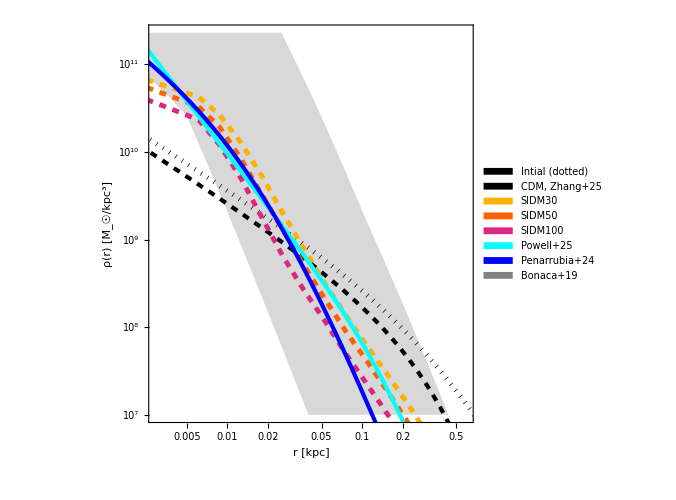

```mathematica
Show[
LogLogPlot[{PertIncloseUp[r],PertIncloseDown[r]},{r,0.0005,20},PlotStyle->Directive[Gray,Thickness[0.00001],Opacity[0.51]],Filling->{1->{2}},FillingStyle->Directive[Opacity[0.3]],PlotRange->{{0.0029,0.6},{10 10^6,2.3 10^11}},
Frame->True,FrameLabel->{{"ρ(r) [M_☉/kpc^3]",None},{"r [kpc]",None}},LabelStyle->{20,GrayLevel[-0.5]},
FrameStyle->Directive[Black,FontFamily->"Times New Roman",FontSize->20,Thickness[0.004]],
FrameTicksStyle->Directive[Black],
ImageSize->500,AspectRatio->1,ImagePadding->{{67,7},{55,5}}]
,
ListLogLogPlot[{NFWinit}~Join~{cdmdata}~Join~{DMrhodataS30}~Join~{DMrhodataS50}~Join~{DMrhodataS100}~Join~{lensingdata2}~Join~{f5data}~Join~{{0,0}},Joined->True,PlotRange->{{0.002,0.2},{0.5 10^7,50 10^10}},
PlotLegends->Placed[SwatchLegend[{"Intial (dotted)","CDM, Zhang+25","SIDM30","SIDM50","SIDM100","Powell+25","Penarrubia+24","Bonaca+19"},LegendMarkerSize->{9,9},LabelStyle->15,LegendLayout->{"Column",1}],{0.84,0.78}],
PlotStyle->{{Black,Dotted,Thickness[0.007]},{Black,Dashed,Thickness[0.006]},{RGBColor["#ffb000"],Dashed,Thickness[0.007]},{RGBColor["#fe6100"], Dashed,Thickness[0.007]},{RGBColor["#dc267f"],Dashed,Thickness[0.007]},{Cyan,Thickness[0.006]},{Blue,Thickness[0.006]},{Gray}},
Frame->True,FrameLabel->{{"ρ(r) [M_☉/kpc^3]",None},{"r [kpc]",None}},LabelStyle->{18,GrayLevel[-0.5]},
FrameStyle->Thickness[0.004],FrameTicksStyle->Directive[Black],ImageSize->500,AspectRatio->1
,ImagePadding->{{67,5},{55,10}}]
]
```